## Мухамадиев Владимир

# Задание 1

## Загрузка и предварительная обработка

```mathematica
data=Import[NotebookDirectory[]<>"\\bio-diseasome.txt","Data"];
```

```mathematica
el=Table[data⟦i,1⟧<->data⟦i,2⟧,{i,1,Length[data]}];
```

```mathematica
g=Graph[el];
```

```mathematica
l={{113,25},{389,20},{457,26},{329,26},{252,26},{66,25},{110,25}};
```

## 1. Чему равно число вершин, число ребер в сети?

```mathematica
VertexCount[g]
```

516

```mathematica
EdgeCount[g]
```

1188

## 2. Является ли сеть направленной?

```mathematica
DirectedGraphQ[g]
```

False

## 3. Чему равна средняя степень вершины?

```mathematica
N[Mean[VertexDegree[g]]]
```

4.60465

## 4. Перечислите узлы с максимальным значением степени.

```mathematica
Module[{in1=ReverseSortBy[{VertexList[g],VertexDegree[g]}ᵀ,Last],in2=Max[VertexDegree[g]],i=0,out={}},While[in1⟦i+1,2⟧==in2,i++];out=in1⟦1;;i,1⟧;out]
```

{93}

## 5. Постройте распределение по степеням связности и огибающую распределения в двойном логарифмическом масштабе.

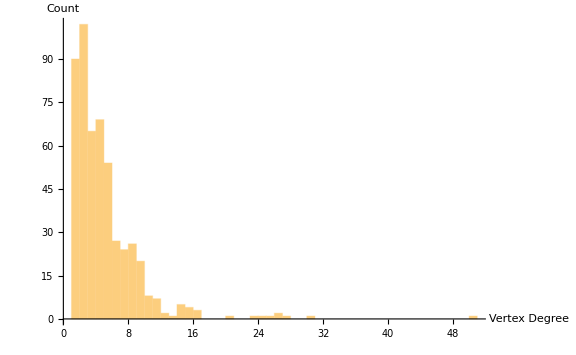

```mathematica
Histogram[VertexDegree[g],PlotRange->All,AxesLabel->{"Vertex Degree","Count"},ImageSize->Large]
```

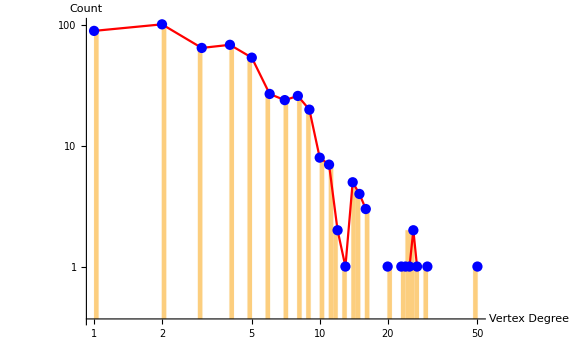

```mathematica
Module[{in1=Histogram[VertexDegree[g],{"Log",Max[VertexDegree[g]]},{"Log","Count"},PlotRange->All,AxesLabel->{"Vertex Degree","Count"},ImageSize->Large],in2={Table[i,{i,1,Max[VertexDegree[g]]}],HistogramList[VertexDegree[g]]⟦2⟧}ᵀ,in3={},out={}},in3=ListLogLogPlot[{in2,in2},Joined->{True,False},PlotStyle->{Red,Blue},PlotRange->All,ImageSize->Large];out=Show[in1,in3];out]
```

## 6. Сколько вершин имеют степень больше 20?

```mathematica
Module[{in=VertexDegree[g],out=0},Do[If[in⟦i⟧>20,out++],{i,0,Length[in]}];out]
```

8

## 7. Каких пар (индекс вершины, степень вершины) нет в вашем списке?

```mathematica
Module[{in1=SortBy[{VertexList[g],VertexDegree[g]}ᵀ,First],in2=SortBy[l,First],out={}},Do[If[in2⟦i⟧≠in1⟦in2⟦i,1⟧⟧,AppendTo[out,in2⟦i⟧]],{i,1,Length[in2]}];out]
```

{{66,25},{110,25},{329,26}}

## 8. Сколько всего треугольников в сети?

```mathematica
Total[Diagonal[MatrixPower[Normal[AdjacencyMatrix[g]],3]]]/6
```

1360

## 9. Чему равен средний коэффициент кластеризации в сети?

```mathematica
N[Mean[LocalClusteringCoefficient[g]]]
```

0.63583

## 10. А чему равен коэффициент транзитивности сети?

```mathematica
N[GlobalClusteringCoefficient[g]]
```

0.430471

## 11. Сколько процентов узлов из имеющих максимальную кластеризацию имеют степень два (т.е. являются вершинами треугольников)?

```mathematica
Module[{in={LocalClusteringCoefficient[g],VertexDegree[g]}ᵀ,n=0,out=0},Do[If[in⟦i,1⟧==1,n++;If[in⟦i,2⟧==2,out++]],{i,1,Length[in]}];out=Quantity[N[out/n 100],"Percent"];out]
```

36.0902 %

## 12. Какова максимальная степень вершины с минимальной кластеризацией?

```mathematica
Module[{in={LocalClusteringCoefficient[g],VertexDegree[g]}ᵀ,out=0},Do[If[in⟦i,1⟧==0&&in⟦i,2⟧>out,out=in⟦i,2⟧],{i,1,Length[in]}];out]
```

5

## 13. Какова кластеризация хаба (вершины с максимальной степенью)?

```mathematica
N[ReverseSortBy[{VertexDegree[g],LocalClusteringCoefficient[g]}ᵀ,First]⟦1,2⟧]
```

0.124082

## 14. Постройте диаграмму рассеяния, по оси X - значение степени узла, по оси Y - его коэффициент кластеризации.

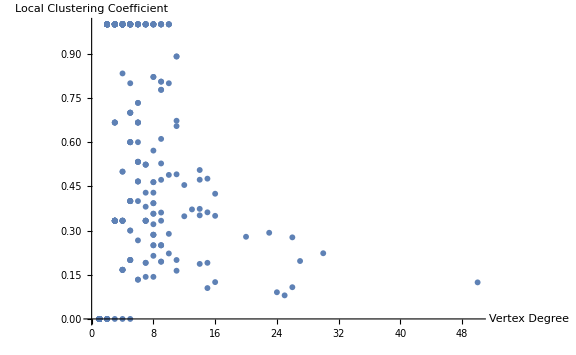

```mathematica
ListPlot[{VertexDegree[g],LocalClusteringCoefficient[g]}ᵀ,PlotRange->All,AxesLabel->{"Vertex Degree","Local\nClustering\nCoefficient"},ImageSize->Large]
```

## 15. Верно ли, что все узлы с кластеризацией, превышающей среднее значение имеют степень меньше 16?

```mathematica
Module[{in1={VertexDegree[g],LocalClusteringCoefficient[g]}ᵀ,in2=Mean[LocalClusteringCoefficient[g]],out=True},Do[If[in1⟦i,1⟧≥16&&in1⟦i,2⟧>in2,out=False],{i,1,Length[in1]}];out]
```

True

## 16. Чему равен средний кратчайший путь в сети?

```mathematica
N[Total[Flatten[GraphDistanceMatrix[g]]]/(VertexCount[g]^2-VertexCount[g])]
```

6.50899

## 17. А чему равен средний путь от хаба до всех остальных вершин?

```mathematica
N[Mean[GraphDistance[g,ReverseSortBy[{VertexList[g],VertexDegree[g]}ᵀ,Last]⟦1,1⟧]]]
```

4.38178

## 18. Чему равен диаметр сети?

```mathematica
GraphDiameter[g]
```

15

## 19. Между какой парой вершин (i,j) число путей длины 4 наибольшее?

```mathematica
Module[{in1=VertexList[g],in2=VertexCount[g],in3=MatrixPower[Normal[AdjacencyMatrix[g]],4],max=0,out={0,0}},Do[If[in3⟦i,j⟧>max&&i≠j,max=in3⟦i,j⟧;out={in1⟦i⟧,in1⟦j⟧}],{i,1,in2},{j,1,in2}];out]
```

{71,93}

## 20. Визуализация сети.

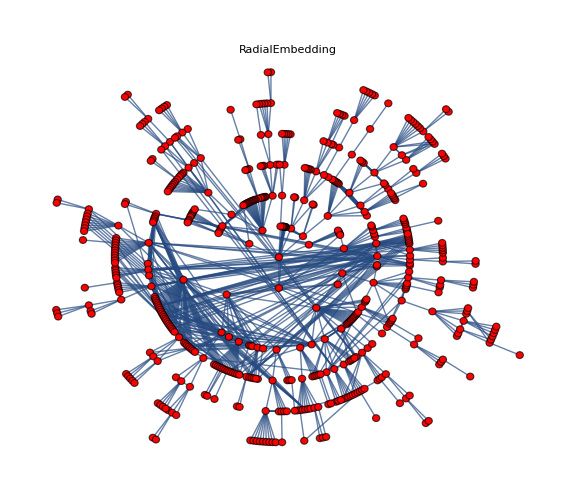
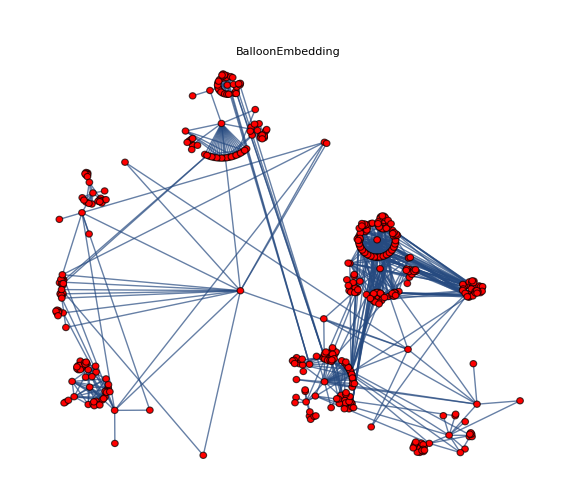
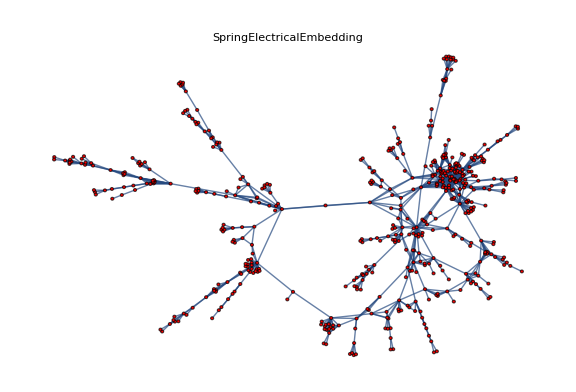

```mathematica
Table[Graph[el,GraphLayout->l,PlotLabel->l,VertexStyle->Red,ImageSize->Large],{l,{"RadialEmbedding","BalloonEmbedding","SpringElectricalEmbedding"}}]
```